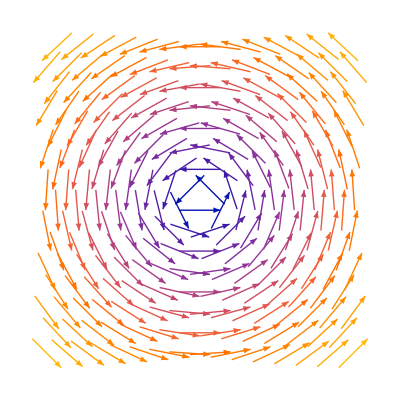

```mathematica
vf2d=VectorPlot[{-y,x},{x,-3,3},{y,-3,3},Frame->False,VectorSizes->2]
```

```mathematica
Export["vf2d.pdf",vf2d,"PDF"]
```

vf2d.pdf

```mathematica
vf3d=VectorPlot3D[{-y,x,z},{x,-3,3},{y,-3,3},{z,-3,3},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["vf3d.pdf",vf3d,"PDF"]
```

vf3d.pdf

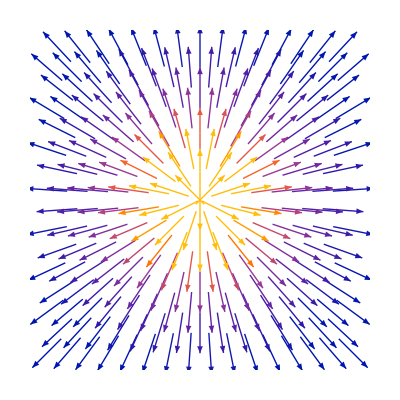

```mathematica
ef2d=VectorPlot[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,-3,3},{y,-3,3},Frame->False,VectorSizes->2]
```

```mathematica
Export["ef2d.pdf",ef2d,"PDF"]
```

ef2d.pdf

```mathematica
ef3d=VectorPlot3D[{x/((x^2+y^2+z^2)^(3/2)),y/((x^2+y^2+z^2)^(3/2)),z/((x^2+y^2+z^2)^(3/2))},{x,-3,3},{y,-3,3},{z,-3,3},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["ef3d.pdf",ef3d,"PDF"]
```

ef3d.pdf

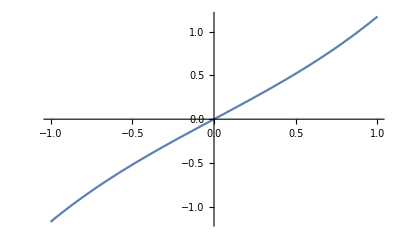

```mathematica
Plot[Sinh[x],{x,-1,1}]
```

```mathematica
d12=Cosh[a1[t]]*Cosh[a2[t]]-Sinh[a1[t]]*Cos[b1[t]]*Sinh[a2[t]]*Cos[b2[t]]-Sinh[a1[t]]*Sin[b1[t]]*Sinh[a2[t]]*Sin[b2[t]]*Cos[g1[t]-g2[t]]
```

Cosh[a1[t]] Cosh[a2[t]]-Cos[b1[t]] Cos[b2[t]] Sinh[a1[t]] Sinh[a2[t]]-Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]] Sinh[a1[t]] Sinh[a2[t]]

```mathematica
dtd12=D[d12,t]//FullSimplify
```

(Cosh[a2[t]] Sinh[a1[t]]-Cosh[a1[t]] (Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a2[t]]) a1'[t]-(Cosh[a2[t]] (Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]]-Cosh[a1[t]] Sinh[a2[t]]) a2'[t]+Sinh[a1[t]] Sinh[a2[t]] ((Cos[b2[t]] Sin[b1[t]]-Cos[b1[t]] Cos[g1[t]-g2[t]] Sin[b2[t]]) b1'[t]+(-Cos[b2[t]] Cos[g1[t]-g2[t]] Sin[b1[t]]+Cos[b1[t]] Sin[b2[t]]) b2'[t]+Sin[b1[t]] Sin[b2[t]] Sin[g1[t]-g2[t]] (g1'[t]-g2'[t]))

```mathematica
da1dtd12 = D[dtd12,a1[t]]//FullSimplify
```

(Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]]) a1'[t]-(Cosh[a1[t]] Cosh[a2[t]] (Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]])-Sinh[a1[t]] Sinh[a2[t]]) a2'[t]+Cosh[a1[t]] Sinh[a2[t]] ((Cos[b2[t]] Sin[b1[t]]-Cos[b1[t]] Cos[g1[t]-g2[t]] Sin[b2[t]]) b1'[t]+(-Cos[b2[t]] Cos[g1[t]-g2[t]] Sin[b1[t]]+Cos[b1[t]] Sin[b2[t]]) b2'[t]+Sin[b1[t]] Sin[b2[t]] Sin[g1[t]-g2[t]] (g1'[t]-g2'[t]))

```mathematica
.5*Sinh[2*.5]
```

0.587601

```mathematica
m1=1;
m2=1;
leq=1;
```

```mathematica
d12=Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]];
dtd12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],t];
dttd12=D[D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],t],t];
da1d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],a1[t]];
db1d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],b1[t]];
dg1d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],g1[t]];
da2d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],a2[t]];
db2d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],b2[t]];
dg2d12=D[Cosh[a1[t]] Cosh[a2[t]]-(Cos[b1[t]] Cos[b2[t]]+Cos[g1[t]-g2[t]] Sin[b1[t]] Sin[b2[t]]) Sinh[a1[t]] Sinh[a2[t]],g2[t]];
```

```mathematica
c1sub={a1[t]->a1c1,b1[t]->b1c1,g1[t]->g1c1,a2[t]->a2c1,b2[t]->b2c1,g2[t]->g2c1,a3[t]->a3c1,b3[t]->b3c1,g3[t]->g3c1,lam->lamc1};
c2sub={a1[t]->a1c2,b1[t]->b1c2,g1[t]->g1c2,a2[t]->a2c2,b2[t]->b2c2,g2[t]->g2c2,a3[t]->a3c2,b3[t]->b3c2,g3[t]->g3c2,lam->lamc2};
```

```mathematica
cona1c1=(lam*da1d12)/(m1*Sqrt[d12^2-1])/.c1sub;
cona1c2=(lam*da1d12)/(m1*Sqrt[d12^2-1])/.c2sub;
conb1c1=(lam*db1d12)/(m1*Sinh[a1[t]]^2 Sqrt[d12^2-1])/.c1sub;
conb1c2=(lam*db1d12)/(m1*Sinh[a1[t]]^2 Sqrt[d12^2-1])/.c2sub;
cong1c1=(lam*dg1d12)/(m1*Sinh[a1[t]]^2*Sin[b1[t]]^2 Sqrt[d12^2-1])/.c1sub;
cong1c2=(lam*dg1d12)/(m1*Sinh[a1[t]]^2*Sin[b1[t]]^2 Sqrt[d12^2-1])/.c2sub;
cona2c1=(lam*da2d12)/(m2*Sqrt[d12^2-1])/.c1sub;
cona2c2=(lam*da2d12)/(m2*Sqrt[d12^2-1])/.c2sub;
conb2c1=(lam*db2d12)/(m2*Sinh[a2[t]]^2 Sqrt[d12^2-1])/.c1sub;
conb2c2=(lam*db2d12)/(m2*Sinh[a2[t]]^2 Sqrt[d12^2-1])/.c2sub;
cong2c1=(lam*dg2d12)/(m2*Sinh[a2[t]]^2*Sin[b2[t]]^2 Sqrt[d12^2-1])/.c1sub;
cong2c2=(lam*dg2d12)/(m2*Sinh[a2[t]]^2*Sin[b2[t]]^2 Sqrt[d12^2-1])/.c2sub;
```

```mathematica
e1=a1c1-a1n-h(a11*ad1c1+a12*ad1c2);
e2=b1c1-b1n-h(a11*bd1c1+a12*bd1c2);
e3=g1c1-g1n-h(a11*gd1c1+a12*gd1c2);

e4=ad1c1-ad1n-h(
a11*(1/2*Sinh[2*a1c1]*(bd1c1^2+gd1c1^2*Sin[b1c1]^2) -cona1c1)+
a12*(1/2*Sinh[2*a1c2]*(bd1c2^2+gd1c2^2*Sin[b1c2]^2)-cona1c2));
e5=bd1c1-bd1n-h(
a11*(-2ad1c1*bd1c1*Coth[a1c1]+.5*Sin[2*b1c1]*gd1c1^2-conb1c1)+
a12*(-2ad1c2*bd1c2*Coth[a1c2]+.5*Sin[2*b1c2]*gd1c2^2-conb1c2));
e6=gd1c1-gd1n-h(
a11*(-2ad1c1*gd1c1*Coth[a1c1]-2bd1c1*gd1c1*Cot[b1c1]-cong1c1)+
a12*(-2ad1c2*gd1c2*Coth[a1c2]-2bd1c2*gd1c2*Cot[b1c2]-cong1c2));

e7=a2c1-a2n-h(a11*ad2c1+a12*ad2c2);
e8=b2c1-b2n-h(a11*bd2c1+a12*bd2c2);
e9=g2c1-g2n-h(a11*gd2c1+a12*gd2c2);

e10=ad2c1-ad2n-h(
a11*(1/2*Sinh[2*a2c1]*(bd2c1^2+gd2c1^2*Sin[b2c1]^2) -cona2c1)+
a12*(1/2*Sinh[2*a2c2]*(bd2c2^2+gd2c2^2*Sin[b2c2]^2)-cona2c2));
e11=bd2c1-bd2n-h(
a11*(-2ad2c1*bd2c1*Coth[a2c1]+.5*Sin[2*b2c1]*gd2c1^2-conb2c1)+
a12*(-2ad2c2*bd2c2*Coth[a2c2]+.5*Sin[2*b2c2]*gd2c2^2-conb2c2));
e12=gd2c1-gd2n-h(
a11*(-2ad2c1*gd2c1*Coth[a2c1]-2bd2c1*gd2c1*Cot[b2c1]-cong2c1)+
a12*(-2ad2c2*gd2c2*Coth[a2c2]-2bd2c2*gd2c2*Cot[b2c2]-cong2c2));

e13=a1c2-a1n-h(a21*ad1c1+a22*ad1c2);
e14=b1c2-b1n-h(a21*bd1c1+a22*bd1c2);
e15=g1c2-g1n-h(a21*gd1c1+a22*gd1c2);

e16=ad1c2-ad1n-h(
a21*(1/2*Sinh[2*a1c1]*(bd1c1^2+gd1c1^2*Sin[b1c1]^2) -cona1c1)+
a22*(1/2*Sinh[2*a1c2]*(bd1c2^2+gd1c2^2*Sin[b1c2]^2)-cona1c2));
e17=bd1c2-bd1n-h(
a21*(-2ad1c1*bd1c1*Coth[a1c1]+.5*Sin[2*b1c1]*gd1c1^2-conb1c1)+
a22*(-2ad1c2*bd1c2*Coth[a1c2]+.5*Sin[2*b1c2]*gd1c2^2-conb1c2));
e18=gd1c2-gd1n-h(
a21*(-2ad1c1*gd1c1*Coth[a1c1]-2bd1c1*gd1c1*Cot[b1c1]-cong1c1)+
a22*(-2ad1c2*gd1c2*Coth[a1c2]-2bd1c2*gd1c2*Cot[b1c2]-cong1c2));

e19=a2c2-a2n-h(a21*ad2c1+a22*ad2c2);
e20=b2c2-b2n-h(a21*bd2c1+a22*bd2c2);
e21=g2c2-g2n-h(a21*gd2c1+a22*gd2c2);

e22=ad2c2-ad2n-h(
a21*(1/2*Sinh[2*a2c1]*(bd2c1^2+gd2c1^2*Sin[b2c1]^2) -cona2c1)+
a22*(1/2*Sinh[2*a2c2]*(bd2c2^2+gd2c2^2*Sin[b2c2]^2)-cona2c2));
e23=bd2c2-bd2n-h(
a21*(-2ad2c1*bd2c1*Coth[a2c1]+.5*Sin[2*b2c1]*gd2c1^2-conb2c1)+
a22*(-2ad2c2*bd2c2*Coth[a2c2]+.5*Sin[2*b2c2]*gd2c2^2-conb2c2));
e24=gd2c2-gd2n-h(
a21*(-2ad2c1*gd2c1*Coth[a2c1]-2bd2c1*gd2c1*Cot[b2c1]-cong2c1)+
a22*(-2ad2c2*gd2c2*Coth[a2c2]-2bd2c2*gd2c2*Cot[b2c2]-cong2c2));

e25=(ArcCosh[d12]-leq)/.c2sub;
e26=(dtd12/Sqrt[d12^2-1])/.{
a1[t]->a1c2,b1[t]->b1c2,g1[t]->g1c2,a2[t]->a2c2,b2[t]->b2c2,g2[t]->g2c2,
a1'[t]->ad1c2,b1'[t]->bd1c2,g1'[t]->gd1c2,a2'[t]->ad2c2,b2'[t]->bd2c2,g2'[t]->gd2c2};
```

```mathematica
conlist={
e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,
e11,e12,e13,e14,e15,e16,e17,e18,e19,e20,
e21,e22,e23,e24,e25,e26
};
dlist={
a1c1,b1c1,g1c1,
ad1c1,bd1c1,gd1c1,
a2c1,b2c1,g2c1,
ad2c1,bd2c1,gd2c1,
a1c2,b1c2,g1c2,
ad1c2,bd1c2,gd1c2,
a2c2,b2c2,g2c2,
ad2c2,bd2c2,gd2c2,
lamc1,lamc2
};
(*dlist={
a1c1,a1c2,
b1c1,b1c2,
g1c1,g1c2,
a2c1,a2c2,
b2c1,b2c2,
g2c1,g2c2,
ad1c1,ad1c2,
bd1c1,bd1c2,
gd1c1,gd1c2,
ad2c1,ad2c2,
bd2c1,bd2c2,
gd2c1,gd2c2,
lamc1,lamc2
};*)

jacmat=Table[D[conlist[[i]],dlist[[j]]],{i,1,Length[conlist]},{j,1,Length[dlist]}];
```

```mathematica
rot2hyp[vec_]:={Sinh[vec[[1]]]Sin[vec[[2]]]Cos[vec[[3]]],Sinh[vec[[1]]]Sin[vec[[2]]]Sin[vec[[3]]],Sinh[vec[[1]]]Cos[vec[[2]]],Cosh[vec[[1]]]};
killingvec[pos_,v_,dir_]:=Module[{hyppos,killingv,ad,bd,gd},
If[dir=="x",
hyppos=rot2hyp[pos];
killingv={v*hyppos[[4]],0,0,v*hyppos[[1]]};
];
If[dir=="y",
hyppos=rot2hyp[pos];
killingv={0,v*hyppos[[4]],0,v*hyppos[[2]]};
];
If[dir=="z",
hyppos=rot2hyp[pos];
killingv={0.,0.,v*hyppos[[4]],v*hyppos[[3]]};
];
ad=killingv[[4]]/Sinh[pos[[1]]];
bd=(ad*Cosh[pos[[1]]]*Cos[pos[[2]]]-killingv[[3]])/(Sinh[pos[[1]]]*Sin[pos[[2]]]);
gd=(killingv[[2]]*Cos[pos[[3]]]-killingv[[1]]*Sin[pos[[3]]])/(Sinh[pos[[1]]]*Sin[pos[[2]]]);
{ad,bd,gd}]
```

```mathematica
hyp2rot[vec_]:={ArcCosh[vec[[4]]],ArcCos[vec[[3]]/Sinh[ArcCosh[vec[[4]]]]],ArcTan[vec[[1]],vec[[2]]]}
rot2hyp[vec_]:={Sinh[vec[[1]]]Sin[vec[[2]]]Cos[vec[[3]]],Sinh[vec[[1]]]Sin[vec[[2]]]Sin[vec[[3]]],Sinh[vec[[1]]]Cos[vec[[2]]],Cosh[vec[[1]]]}
hypnorm[vec_]:=Sqrt[-vec[[1]]^2-vec[[2]]^2-vec[[3]]^2+vec[[4]]^2]
rotnorm[pos_,vec_]:=Sqrt[vec[[1]]^2+vec[[2]]^2 Sinh[pos[[1]]]^2+vec[[3]]^2 Sinh[pos[[1]]]^2 Sin[pos[[2]]]^2]
bx[b_]:={
{Cosh[b],0,0,Sinh[b]},
{0,1,0,0},
{0,0,1,0},
{Sinh[b],0,0,Cosh[b]}
}
ry[b_]:={
{Cos[b],0,Sin[b],0},
{0,1,0,0},
{-Sin[b],0,Cos[b],0},
{0,0,0,1}
}
rz[b_]:={
{Cos[b],-Sin[b],0,0},
{Sin[b],Cos[b],0,0},
{0,0,1,0},
{0,0,0,1}
}
```

```mathematica
startpos={{.5,π/2,π/2},{.5,π/2,(3π)/2}};
v=1;
(*startvel={{0,0,-1},{0,0,1}};*)
startvel={killingvec[startpos[[1]],v,"x"],killingvec[startpos[[2]],v,"x"]};
initvec={
startpos[[1]][[1]],startpos[[1]][[2]],startpos[[1]][[3]],
startvel[[1]][[1]],startvel[[1]][[2]],startvel[[1]][[3]],
startpos[[2]][[1]],startpos[[2]][[2]],startpos[[2]][[3]],
startvel[[2]][[1]],startvel[[2]][[2]],startvel[[2]][[3]],

startpos[[1]][[1]],startpos[[1]][[2]],startpos[[1]][[3]],
startvel[[1]][[1]],startvel[[1]][[2]],startvel[[1]][[3]],
startpos[[2]][[1]],startpos[[2]][[2]],startpos[[2]][[3]],
startvel[[2]][[1]],startvel[[2]][[2]],startvel[[2]][[3]],

0.,0.
};
h=.001;
tmax=1;
m1=1;
m2=1;
a11=5/12;a12=-1/12;
a21=3/4;a22=1/4;
data={};
AppendTo[data,N[initvec]];
step=1.;
nump=1.(*tmax/h//IntegerPart*);
(*pnump=1/h//IntegerPart;*)
While[step≤ nump,
jmat1=jacmat/.{
a1c1->initvec[[1]],b1c1->initvec[[2]],g1c1->initvec[[3]],
ad1c1->initvec[[4]],bd1c1->initvec[[5]],gd1c1->initvec[[6]],
a2c1->initvec[[7]],b2c1->initvec[[8]],g2c1->initvec[[9]],
ad2c1->initvec[[10]],bd2c1->initvec[[11]],gd2c1->initvec[[12]],

a1c2->initvec[[13]],b1c2->initvec[[14]],g1c2->initvec[[15]],
ad1c2->initvec[[16]],bd1c2->initvec[[17]],gd1c2->initvec[[18]],
a2c2->initvec[[19]],b2c2->initvec[[20]],g2c2->initvec[[21]],
ad2c2->initvec[[22]],bd2c2->initvec[[23]],gd2c2->initvec[[24]],

lamc1->initvec[[25]],lamc2->initvec[[26]]
};
Print["Iteration 1 conlist"];
Print[conlist/.{
a1n->initvec[[1]],b1n->initvec[[2]],g1n->initvec[[3]],
ad1n->initvec[[4]],bd1n->initvec[[5]],gd1n->initvec[[6]],
a2n->initvec[[7]],b2n->initvec[[8]],g2n->initvec[[9]],
ad2n->initvec[[10]],bd2n->initvec[[11]],gd2n->initvec[[12]],

a1c1->initvec[[1]],b1c1->initvec[[2]],g1c1->initvec[[3]],
ad1c1->initvec[[4]],bd1c1->initvec[[5]],gd1c1->initvec[[6]],
a2c1->initvec[[7]],b2c1->initvec[[8]],g2c1->initvec[[9]],
ad2c1->initvec[[10]],bd2c1->initvec[[11]],gd2c1->initvec[[12]],

a1c2->initvec[[13]],b1c2->initvec[[14]],g1c2->initvec[[15]],
ad1c2->initvec[[16]],bd1c2->initvec[[17]],gd1c2->initvec[[18]],
a2c2->initvec[[19]],b2c2->initvec[[20]],g2c2->initvec[[21]],
ad2c2->initvec[[22]],bd2c2->initvec[[23]],gd2c2->initvec[[24]],

lamc1->initvec[[25]],lamc2->initvec[[26]]
}];
Print["Iteration 1 jacobian"];
Print[jmat1//MatrixForm];
diff1=LinearSolve[jmat1,(-conlist/.{
a1n->initvec[[1]],b1n->initvec[[2]],g1n->initvec[[3]],
ad1n->initvec[[4]],bd1n->initvec[[5]],gd1n->initvec[[6]],
a2n->initvec[[7]],b2n->initvec[[8]],g2n->initvec[[9]],
ad2n->initvec[[10]],bd2n->initvec[[11]],gd2n->initvec[[12]],

a1c1->initvec[[1]],b1c1->initvec[[2]],g1c1->initvec[[3]],
ad1c1->initvec[[4]],bd1c1->initvec[[5]],gd1c1->initvec[[6]],
a2c1->initvec[[7]],b2c1->initvec[[8]],g2c1->initvec[[9]],
ad2c1->initvec[[10]],bd2c1->initvec[[11]],gd2c1->initvec[[12]],

a1c2->initvec[[13]],b1c2->initvec[[14]],g1c2->initvec[[15]],
ad1c2->initvec[[16]],bd1c2->initvec[[17]],gd1c2->initvec[[18]],
a2c2->initvec[[19]],b2c2->initvec[[20]],g2c2->initvec[[21]],
ad2c2->initvec[[22]],bd2c2->initvec[[23]],gd2c2->initvec[[24]],

lamc1->initvec[[25]],lamc2->initvec[[26]]
})];
Print["Iteration 1 solution vector"];
Print[diff1];
val1=diff1+initvec;
Print["Iteration 2 data"];
Print[val1];
Print["Iteration 2 k1"];
Print[(1/2*Sinh[2*a1c1]*(bd1c1^2+gd1c1^2*Sin[b1c1]^2) -cona1c1)/.{
a1n->initvec[[1]],b1n->initvec[[2]],g1n->initvec[[3]],
ad1n->initvec[[4]],bd1n->initvec[[5]],gd1n->initvec[[6]],
a2n->initvec[[7]],b2n->initvec[[8]],g2n->initvec[[9]],
ad2n->initvec[[10]],bd2n->initvec[[11]],gd2n->initvec[[12]],

a1c1->val1[[1]],b1c1->val1[[2]],g1c1->val1[[3]],
ad1c1->val1[[4]],bd1c1->val1[[5]],gd1c1->val1[[6]],
a2c1->val1[[7]],b2c1->val1[[8]],g2c1->val1[[9]],
ad2c1->val1[[10]],bd2c1->val1[[11]],gd2c1->val1[[12]],

a1c2->val1[[13]],b1c2->val1[[14]],g1c2->val1[[15]],
ad1c2->val1[[16]],bd1c2->val1[[17]],gd1c2->val1[[18]],
a2c2->val1[[19]],b2c2->val1[[20]],g2c2->val1[[21]],
ad2c2->val1[[22]],bd2c2->val1[[23]],gd2c2->val1[[24]],

lamc1->val1[[25]],lamc2->val1[[26]]
}];
Print["Iteration 2 conlist"];
Print[conlist/.{
a1n->initvec[[1]],b1n->initvec[[2]],g1n->initvec[[3]],
ad1n->initvec[[4]],bd1n->initvec[[5]],gd1n->initvec[[6]],
a2n->initvec[[7]],b2n->initvec[[8]],g2n->initvec[[9]],
ad2n->initvec[[10]],bd2n->initvec[[11]],gd2n->initvec[[12]],

a1c1->val1[[1]],b1c1->val1[[2]],g1c1->val1[[3]],
ad1c1->val1[[4]],bd1c1->val1[[5]],gd1c1->val1[[6]],
a2c1->val1[[7]],b2c1->val1[[8]],g2c1->val1[[9]],
ad2c1->val1[[10]],bd2c1->val1[[11]],gd2c1->val1[[12]],

a1c2->val1[[13]],b1c2->val1[[14]],g1c2->val1[[15]],
ad1c2->val1[[16]],bd1c2->val1[[17]],gd1c2->val1[[18]],
a2c2->val1[[19]],b2c2->val1[[20]],g2c2->val1[[21]],
ad2c2->val1[[22]],bd2c2->val1[[23]],gd2c2->val1[[24]],

lamc1->val1[[25]],lamc2->val1[[26]]
}];
q=0;
(*Print[Norm[diff1]];*)
While[Norm[diff1]>10^-8&&q<1(*00*),
jmat2=jacmat/.{
a1c1->val1[[1]],b1c1->val1[[2]],g1c1->val1[[3]],
ad1c1->val1[[4]],bd1c1->val1[[5]],gd1c1->val1[[6]],
a2c1->val1[[7]],b2c1->val1[[8]],g2c1->val1[[9]],
ad2c1->val1[[10]],bd2c1->val1[[11]],gd2c1->val1[[12]],

a1c2->val1[[13]],b1c2->val1[[14]],g1c2->val1[[15]],
ad1c2->val1[[16]],bd1c2->val1[[17]],gd1c2->val1[[18]],
a2c2->val1[[19]],b2c2->val1[[20]],g2c2->val1[[21]],
ad2c2->val1[[22]],bd2c2->val1[[23]],gd2c2->val1[[24]],

lamc1->val1[[25]],lamc2->val1[[26]]
};
Print[jmat2//MatrixForm];
diff2=LinearSolve[jmat2,(-conlist/.{
a1n->initvec[[1]],b1n->initvec[[2]],g1n->initvec[[3]],
ad1n->initvec[[4]],bd1n->initvec[[5]],gd1n->initvec[[6]],
a2n->initvec[[7]],b2n->initvec[[8]],g2n->initvec[[9]],
ad2n->initvec[[10]],bd2n->initvec[[11]],gd2n->initvec[[12]],

a1c1->val1[[1]],b1c1->val1[[2]],g1c1->val1[[3]],
ad1c1->val1[[4]],bd1c1->val1[[5]],gd1c1->val1[[6]],
a2c1->val1[[7]],b2c1->val1[[8]],g2c1->val1[[9]],
ad2c1->val1[[10]],bd2c1->val1[[11]],gd2c1->val1[[12]],

a1c2->val1[[13]],b1c2->val1[[14]],g1c2->val1[[15]],
ad1c2->val1[[16]],bd1c2->val1[[17]],gd1c2->val1[[18]],
a2c2->val1[[19]],b2c2->val1[[20]],g2c2->val1[[21]],
ad2c2->val1[[22]],bd2c2->val1[[23]],gd2c2->val1[[24]],

lamc1->val1[[25]],lamc2->val1[[26]]
})];
Print[diff2];
val2=val1+diff2;
val1=val2;
diff1=diff2;
Print[Norm[diff1]];
q++];
Print[val1];
AppendTo[data,N[val1]];
initvec={
val1[[13]],val1[[14]],val1[[15]],
val1[[16]],val1[[17]],val1[[18]],
val1[[19]],val1[[20]],val1[[21]],
val1[[22]],val1[[23]],val1[[24]],

val1[[13]],val1[[14]],val1[[15]],
val1[[16]],val1[[17]],val1[[18]],
val1[[19]],val1[[20]],val1[[21]],
val1[[22]],val1[[23]],val1[[24]],

val1[[26]],val1[[26]]
};
If[Mod[step,pnump]==0,Print[step]];
step++];
```

Iteration 1 conlist

{0.,0.,0.000721318,-0.000917185,0.,0.,0.,0.,-0.000721318,-0.000917185,0.,0.,0.,0.,0.00216395,-0.00275155,0.,0.,0.,0.,-0.00216395,-0.00275155,0.,0.,-2.22045×10^-16,0.}

Iteration 1 jacobian

(1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00301074 | 0. | 0. | 1 | 0. | 0.00105962 | 0. | 0. | 0. | 0 | 0 | 0 | 0.000602148 | 0. | 0. | 0 | 0. | -0.000211923 | 0. | 0. | 0. | 0 | 0 | 0 | 0.000416667 | -0.0000833333
0. | 0.00195112 | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | -0.000390225 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.
0. | 0. | 0. | -0.00390225 | 0. | 1. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0.000780449 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0
0. | 0. | 0. | 0 | 0 | 0 | -0.00301074 | 0. | 0. | 1 | 0. | -0.00105962 | 0. | 0. | 0. | 0 | 0 | 0 | 0.000602148 | 0. | 0. | 0 | 0. | 0.000211923 | 0.000416667 | -0.0000833333
0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.00195112 | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | -0.000390225 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0.00390225 | 0. | 1. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | -0.000780449 | 0. | 0. | 0. | 0.
0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00541933 | 0. | 0. | 0 | 0. | 0.00190731 | 0. | 0. | 0. | 0 | 0 | 0 | -0.00180644 | 0. | 0. | 1 | 0. | 0.00063577 | 0. | 0. | 0. | 0 | 0 | 0 | 0.00075 | 0.00025
0. | 0.00351202 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.00117067 | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.
0. | 0. | 0. | -0.00702404 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | -0.00234135 | 0. | 1. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0
0. | 0. | 0. | 0 | 0 | 0 | -0.00541933 | 0. | 0. | 0 | 0. | -0.00190731 | 0. | 0. | 0. | 0 | 0 | 0 | -0.00180644 | 0. | 0. | 1 | 0. | -0.00063577 | 0.00075 | 0.00025
0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.00351202 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0.00117067 | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0.00702404 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0.00234135 | 0. | 1. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0. | 0. | 0 | 0 | 0 | 1. | 0. | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | -1. | 1. | 0. | 0. | 0 | 0)

Iteration 1 solution vector

{-4.80879×10^-7,0.,-0.00072132,-0.000721319,0.,-4.50362×10^-6,-4.80879×10^-7,0.,0.00072132,-0.000721319,0.,4.50362×10^-6,1.11022×10^-16,0.,-0.00216396,0.00216396,0.,1.03977×10^-15,1.11022×10^-16,0.,0.00216396,0.00216396,0.,-1.03977×10^-15,2.75156,-5.90427}

Iteration 2 data

{0.5,1.5708,1.57008,-0.000721319,0.,-2.16396,0.5,1.5708,4.71311,-0.000721319,0.,2.16396,0.5,1.5708,1.56863,0.00216396,0.,-2.16395,0.5,1.5708,4.71455,0.00216396,0.,2.16395,2.75156,-5.90427}

Iteration 2 conlist

{-1.76912×10^-17,0.,0.,-1.14055×10^-9,7.51667×10^-20,3.21937×10^-6,-1.76912×10^-17,0.,0.,-1.14055×10^-9,7.51667×10^-20,-3.21937×10^-6,2.1684×10^-22,0.,-2.22045×10^-16,2.29575×10^-9,-2.255×10^-19,-2.9026×10^-6,2.1684×10^-22,0.,0.,2.29575×10^-9,-2.255×10^-19,2.9026×10^-6,-2.16396×10^-6,-6.75545×10^-9}

(1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00301075 | -1.12799×10^-19 | 3.25189×10^-7 | 1 | 0. | 0.00105962 | -3.99192×10^-10 | 2.76051×10^-20 | -3.25189×10^-7 | 0 | 0 | 0 | 0.00060215 | 3.99276×10^-20 | 4.18672×10^-7 | 0 | 0. | -0.000211923 | -1.54185×10^-9 | 1.18469×10^-20 | -4.18672×10^-7 | 0 | 0 | 0 | 0.000416667 | -0.0000833332
-4.15404×10^-19 | 0.000975566 | 3.38872×10^-23 | 0. | 0.999999 | 1.1042×10^-19 | 1.01661×10^-19 | -0.000975566 | -3.38872×10^-23 | 0 | 0 | 0 | -1.78273×10^-19 | -0.000808893 | 4.36287×10^-23 | 0. | -7.8045×10^-7 | -2.2084×10^-20 | 4.36286×10^-20 | -0.000418672 | -4.36287×10^-23 | 0 | 0 | 0 | 4.34198×10^-20 | -8.68394×10^-21
-9.68377×10^-6 | -1.38468×10^-22 | -0.000975565 | -0.00390226 | -1.1042×10^-19 | 0.999999 | 1.19757×10^-6 | 3.38872×10^-23 | 0.000975565 | 0 | 0 | 0 | -9.17436×10^-6 | -1.78274×10^-22 | -0.000418671 | 0.000780449 | 2.2084×10^-20 | -7.8045×10^-7 | 1.54184×10^-6 | 4.36287×10^-23 | 0.000418671 | 0 | 0 | 0 | 5.11487×10^-7 | -3.06892×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.000416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000833333 | 0 | 0
-3.99192×10^-10 | 2.76051×10^-20 | 3.25189×10^-7 | 0 | 0 | 0 | -0.00301075 | -1.12799×10^-19 | -3.25189×10^-7 | 1 | 0. | -0.00105962 | -1.54185×10^-9 | 1.18469×10^-20 | 4.18672×10^-7 | 0 | 0 | 0 | 0.00060215 | 3.99276×10^-20 | -4.18672×10^-7 | 0 | 0. | 0.000211923 | 0.000416667 | -0.0000833332
1.01661×10^-19 | -0.000975566 | 3.38872×10^-23 | 0 | 0 | 0 | -4.15404×10^-19 | 0.000975566 | -3.38872×10^-23 | 0. | 0.999999 | -1.1042×10^-19 | 4.36286×10^-20 | -0.000418672 | 4.36287×10^-23 | 0 | 0 | 0 | -1.78273×10^-19 | -0.000808893 | -4.36287×10^-23 | 0. | -7.8045×10^-7 | 2.2084×10^-20 | 4.34198×10^-20 | -8.68394×10^-21
-1.19757×10^-6 | -3.38872×10^-23 | 0.000975565 | 0 | 0 | 0 | 9.68377×10^-6 | 1.38468×10^-22 | -0.000975565 | 0.00390226 | 1.1042×10^-19 | 0.999999 | -1.54184×10^-6 | -4.36287×10^-23 | 0.000418671 | 0 | 0 | 0 | 9.17436×10^-6 | 1.78274×10^-22 | -0.000418671 | -0.000780449 | -2.2084×10^-20 | -7.8045×10^-7 | -5.11487×10^-7 | 3.06892×10^-7
0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00541935 | -2.03038×10^-19 | 5.8534×10^-7 | 0 | 0. | 0.00190731 | -7.18546×10^-10 | 4.96891×10^-20 | -5.8534×10^-7 | 0 | 0 | 0 | -0.00180645 | -1.19783×10^-19 | -1.25602×10^-6 | 1 | 0. | 0.00063577 | 4.62554×10^-9 | -3.55408×10^-20 | 1.25602×10^-6 | 0 | 0 | 0 | 0.00075 | 0.00025
-7.47727×10^-19 | 0.00175602 | 6.09969×10^-23 | 0. | -2.34135×10^-6 | 1.98756×10^-19 | 1.8299×10^-19 | -0.00175602 | -6.09969×10^-23 | 0 | 0 | 0 | 5.3482×10^-19 | 0.00242668 | -1.30886×10^-22 | 0. | 1. | 6.6252×10^-20 | -1.30886×10^-19 | 0.00125602 | 1.30886×10^-22 | 0 | 0 | 0 | 7.81556×10^-20 | 2.60518×10^-20
-0.0000174308 | -2.49243×10^-22 | -0.00175602 | -0.00702406 | -1.98756×10^-19 | -2.34135×10^-6 | 2.15563×10^-6 | 6.09969×10^-23 | 0.00175602 | 0 | 0 | 0 | 0.0000275231 | 5.34821×10^-22 | 0.00125601 | -0.00234135 | -6.6252×10^-20 | 1. | -4.62552×10^-6 | -1.30886×10^-22 | -0.00125601 | 0 | 0 | 0 | 9.20677×10^-7 | 9.20675×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -0.00025 | 0 | 0
-7.18546×10^-10 | 4.96891×10^-20 | 5.8534×10^-7 | 0 | 0 | 0 | -0.00541935 | -2.03038×10^-19 | -5.8534×10^-7 | 0 | 0. | -0.00190731 | 4.62554×10^-9 | -3.55408×10^-20 | -1.25602×10^-6 | 0 | 0 | 0 | -0.00180645 | -1.19783×10^-19 | 1.25602×10^-6 | 1 | 0. | -0.00063577 | 0.00075 | 0.00025
1.8299×10^-19 | -0.00175602 | 6.09969×10^-23 | 0 | 0 | 0 | -7.47727×10^-19 | 0.00175602 | -6.09969×10^-23 | 0. | -2.34135×10^-6 | -1.98756×10^-19 | -1.30886×10^-19 | 0.00125602 | -1.30886×10^-22 | 0 | 0 | 0 | 5.3482×10^-19 | 0.00242668 | 1.30886×10^-22 | 0. | 1. | -6.6252×10^-20 | 7.81556×10^-20 | 2.60518×10^-20
-2.15563×10^-6 | -6.09969×10^-23 | 0.00175602 | 0 | 0 | 0 | 0.0000174308 | 2.49243×10^-22 | -0.00175602 | 0.00702406 | 1.98756×10^-19 | -2.34135×10^-6 | 4.62552×10^-6 | 1.30886×10^-22 | -0.00125601 | 0 | 0 | 0 | -0.0000275231 | -5.34821×10^-22 | 0.00125601 | 0.00234135 | 6.6252×10^-20 | 1. | -9.20677×10^-7 | -9.20675×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999998 | 2.82965×10^-17 | 0.001 | 0 | 0 | 0 | 0.999998 | 2.82965×10^-17 | -0.001 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0036827 | -1.62658×10^-25 | 1. | 0.999998 | 2.82965×10^-17 | 0.001 | -0.0036827 | -1.62658×10^-25 | -1. | 0.999998 | 2.82965×10^-17 | -0.001 | 0 | 0)

{6.01099×10^-7,1.25282×10^-23,1.5413×10^-9,0.00144264,7.51674×10^-20,5.50935×10^-6,6.01099×10^-7,1.25282×10^-23,-1.5413×10^-9,0.00144264,7.51674×10^-20,-5.50935×10^-6,1.08198×10^-6,1.1275×10^-22,6.39479×10^-9,-8.08365×10^-9,2.25498×10^-19,9.05112×10^-6,1.08198×10^-6,1.1275×10^-22,-6.39479×10^-9,-8.08365×10^-9,2.25498×10^-19,-9.05112×10^-6,-2.16396,6.49187}

6.84303

{0.5,1.5708,1.57008,0.000721318,7.51674×10^-20,-2.16395,0.5,1.5708,4.71311,0.000721318,7.51674×10^-20,2.16395,0.500001,1.5708,1.56863,0.00216395,2.25498×10^-19,-2.16394,0.500001,1.5708,4.71455,0.00216395,2.25498×10^-19,2.16394,0.587601,0.587598}

```mathematica
(conlist/.{
a1n->initvec[[1]],b1n->initvec[[3]],g1n->initvec[[5]],
a2n->initvec[[7]],b2n->initvec[[9]],g2n->initvec[[11]],
ad1n->initvec[[13]],bd1n->initvec[[15]],gd1n->initvec[[17]],
ad2n->initvec[[19]],bd2n->initvec[[21]],gd2n->initvec[[23]],

a1c1->initvec[[1]],a1c2->initvec[[2]],
b1c1->initvec[[3]],b1c2->initvec[[4]],
g1c1->initvec[[5]],g1c2->initvec[[6]],
a2c1->initvec[[7]],a2c2->initvec[[8]],
b2c1->initvec[[9]],b2c2->initvec[[10]],
g2c1->initvec[[11]],g2c2->initvec[[12]],

ad1c1->initvec[[13]],ad1c2->initvec[[14]],
bd1c1->initvec[[15]],bd1c2->initvec[[16]],
gd1c1->initvec[[17]],gd1c2->initvec[[18]],
ad2c1->initvec[[19]],ad2c2->initvec[[20]],
bd2c1->initvec[[21]],bd2c2->initvec[[22]],
gd2c1->initvec[[23]],gd2c2->initvec[[24]],

lamc1->initvec[[25]],lamc2->initvec[[26]]
})
```

{0.,0.,0.,0.,0.000211325,0.000788675,0.,0.,0.,0.,-0.000211325,-0.000788675,-0.000124175,-0.000463426,0.,0.,0.,0.,-0.000124175,-0.000463426,0.,0.,0.,0.,-2.22045×10^-16,0.}

```mathematica
D[Coth[x],x]
```

-Csch[x]^2

```mathematica
data=BinaryReadList["np.dat","Real64"];
```

```mathematica
data
```

{1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,-0.00301073,-1.40403×10^-19,0.,1.,0.,0.00105962,0.,0.,0.,0.,0.,0.,0.000602146,2.80806×10^-20,0.,0.,0.,-0.000211923,0.,0.,0.,0.,0.,0.,0.000416667,-0.0000833333,0.,0.00195112,0.,0.,1.,1.1042×10^-19,0.,0.,0.,0.,0.,0.,0.,-0.000390223,0.,0.,0.,-2.2084×10^-20,0.,0.,0.,0.,0.,0.,4.34198×10^-20,-8.68395×10^-21,0.,0.,0.,-0.00390224,-1.1042×10^-19,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000780448,2.2084×10^-20,0.,0.,0.,0.,0.,0.,0.,-4.34198×10^-20,8.68395×10^-21,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.000416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.,-0.00301073,-1.40403×10^-19,0.,1.,0.,-0.00105962,0.,0.,0.,0.,0.,0.,0.000602146,2.80806×10^-20,0.,0.,0.,0.000211923,0.000416667,-0.0000833333,0.,0.,0.,0.,0.,0.,0.,0.00195112,0.,0.,1.,-1.1042×10^-19,0.,0.,0.,0.,0.,0.,0.,-0.000390223,0.,0.,0.,2.2084×10^-20,4.34198×10^-20,-8.68395×10^-21,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00390224,1.1042×10^-19,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000780448,-2.2084×10^-20,0.,4.34198×10^-20,-8.68395×10^-21,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,-0.00541931,-2.52725×10^-19,0.,0.,0.,0.00190731,0.,0.,0.,0.,0.,0.,-0.00180644,-8.42418×10^-20,0.,1.,0.,0.000635769,0.,0.,0.,0.,0.,0.,0.00075,0.00025,0.,0.00351201,0.,0.,0.,1.98756×10^-19,0.,0.,0.,0.,0.,0.,0.,0.00117067,0.,0.,1.,6.62519×10^-20,0.,0.,0.,0.,0.,0.,7.81556×10^-20,2.60519×10^-20,0.,0.,0.,-0.00702403,-1.98756×10^-19,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00234134,-6.62519×10^-20,1.,0.,0.,0.,0.,0.,0.,-7.81556×10^-20,-2.60519×10^-20,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00075,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.00025,0.,0.,0.,0.,0.,0.,0.,0.,-0.00541931,-2.52725×10^-19,0.,0.,0.,-0.00190731,0.,0.,0.,0.,0.,0.,-0.00180644,-8.42418×10^-20,0.,1.,0.,-0.000635769,0.00075,0.00025,0.,0.,0.,0.,0.,0.,0.,0.00351201,0.,0.,0.,-1.98756×10^-19,0.,0.,0.,0.,0.,0.,0.,0.00117067,0.,0.,1.,-6.62519×10^-20,7.81556×10^-20,2.60519×10^-20,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00702403,1.98756×10^-19,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00234134,6.62519×10^-20,1.,7.81556×10^-20,2.60519×10^-20,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,2.82965×10^-17,-2.82965×10^-17,0.,0.,0.,1.,2.82965×10^-17,2.82965×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.04207×10^-16,2.9487×10^-33,0.999998,1.,2.82965×10^-17,-2.82965×10^-17,1.04207×10^-16,2.9487×10^-33,-0.999998,1.,2.82965×10^-17,2.82965×10^-17,0.,0.}

```mathematica
Flatten[jmat1]
```

{1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0,0,0,0,0,0,-0.00301074,0.,0.,1,0.,0.00105962,0.,0.,0.,0,0,0,0.000602148,0.,0.,0,0.,-0.000211923,0.,0.,0.,0,0,0,0.000416667,-0.0000833333,0.,0.00195112,0.,0.,1.,0.,0.,0.,0.,0,0,0,0.,-0.000390225,0.,0.,0.,0.,0.,0.,0.,0,0,0,0.,0.,0.,0.,0.,-0.00390225,0.,1.,0.,0.,0.,0,0,0,0.,0.,0.,0.000780449,0.,0.,0.,0.,0.,0,0,0,0.,0.,0,0,0,0,0,0,1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-0.000416667,0,0,0,0,0,0,0,0,0,0,0,0.0000833333,0,0,0.,0.,0.,0,0,0,-0.00301074,0.,0.,1,0.,-0.00105962,0.,0.,0.,0,0,0,0.000602148,0.,0.,0,0.,0.000211923,0.000416667,-0.0000833333,0.,0.,0.,0,0,0,0.,0.00195112,0.,0.,1.,0.,0.,0.,0.,0,0,0,0.,-0.000390225,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0.,0.,0.,0.00390225,0.,1.,0.,0.,0.,0,0,0,0.,0.,0.,-0.000780449,0.,0.,0.,0.,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0,0,0,0,0,0,-0.00541933,0.,0.,0,0.,0.00190731,0.,0.,0.,0,0,0,-0.00180644,0.,0.,1,0.,0.00063577,0.,0.,0.,0,0,0,0.00075,0.00025,0.,0.00351202,0.,0.,0.,0.,0.,0.,0.,0,0,0,0.,0.00117067,0.,0.,1.,0.,0.,0.,0.,0,0,0,0.,0.,0.,0.,0.,-0.00702404,0.,0.,0.,0.,0.,0,0,0,0.,0.,0.,-0.00234135,0.,1.,0.,0.,0.,0,0,0,0.,0.,0,0,0,0,0,0,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00075,0,0,0,0,0,0,0,0,1,0,0,-0.00025,0,0,0.,0.,0.,0,0,0,-0.00541933,0.,0.,0,0.,-0.00190731,0.,0.,0.,0,0,0,-0.00180644,0.,0.,1,0.,-0.00063577,0.00075,0.00025,0.,0.,0.,0,0,0,0.,0.00351202,0.,0.,0.,0.,0.,0.,0.,0,0,0,0.,0.00117067,0.,0.,1.,0.,0.,0.,0.,0.,0.,0,0,0,0.,0.,0.,0.00702404,0.,0.,0.,0.,0.,0,0,0,0.,0.,0.,0.00234135,0.,1.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,1.,0.,0.,0,0,0,1.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.,1.,0.,0.,0.,0.,-1.,1.,0.,0.,0,0}

```mathematica
beep=3;
(Flatten[jmat1]-data)[[26*beep;;26*(beep+1)]]//MatrixForm
```

(0.
-9.49916×10^-9
1.40403×10^-19
0.
0.
0.
1.6716×10^-9
0.
0.
0.
0.
0.
0.
1.89983×10^-9
-2.80806×10^-20
0.
0.
0.
-3.34319×10^-10
0.
0.
0.
0.
0.
0.
0.
0.)